```mathematica
makeVerPoly[lv_,d_]:=(Subscript[x, #]^d-1)&/@lv;
notEqualPoly[vx_,vy_,d_]:=Factor[(vx^d-vy^d)/(vx-vy)];
makeAdyPoly[le_,d_]:=notEqualPoly[Subscript[x, #[[1]]],Subscript[x, #[[2]]],d]&/@le;
makeGraphPoly[g_Graph,d_Integer]:=Join[makeVerPoly[VertexList[g],d],makeAdyPoly[EdgeList[g],d]];
```

```mathematica
listVariables[l_]:=Subscript[x,#]&/@l;
graphGroebnerBase[g_Graph,d_Integer]:= GroebnerBasis[makeGraphPoly[g,d],listVariables[VertexList[g]]];
```

```mathematica
makeEquation[lp_]:=#==0&/@lp;
possibleCol[g_Graph,d_Integer] :=Solve[makeEquation[graphGroebnerBase[g,d]],listVariables[VertexList[g]]];
countSol[g_Graph,d_Integer]:=Length[possibleCol[g,d]];
countDCol[g_Graph,d_Integer]:= (
var= countSol[g,d];
If[var==0,Print["No es ",d,"-coloreable"],var]
);
```

```mathematica
colors = {Green,Yellow,Red,Black,White,Gray,Purple,Blue,Green,Orange,Gray};
unityRoots[d_] := Cos[2π*#/d] + ⅈ*Sin[2π*#/d]& /@Range[d];
firstPosition[l_,f_]:=FirstPosition[l,SelectFirst[l,f]];
rootToColor[x_,d_]:=colors[[firstPosition[unityRoots[d],FullSimplify[x]==#&]]];
genColRule[r_,d_,s_]:=(#->rootToColor[Subscript[x, #]/.r,d])&/@Range[s];colorGraph[g_Graph,r_,d_]:=Graph[EdgeList[g],VertexStyle->genColRule[r,d,VertexCount[g]]];
allColorGraph[g_Graph,d_Integer]:=colorGraph[g,#,d]&/@possibleCol[g,d];
```

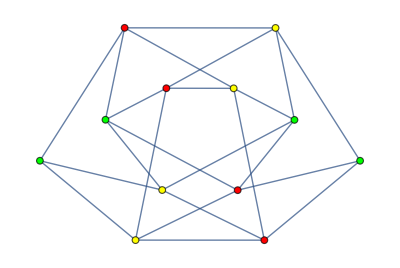

```mathematica
allColorGraph[G,3][[1]]
```

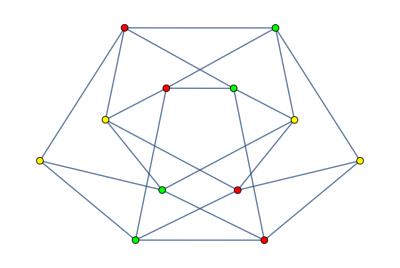
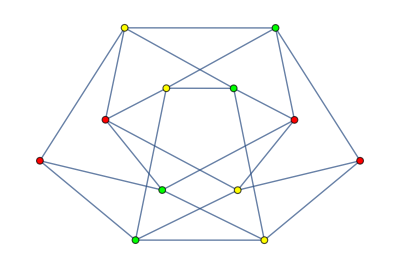
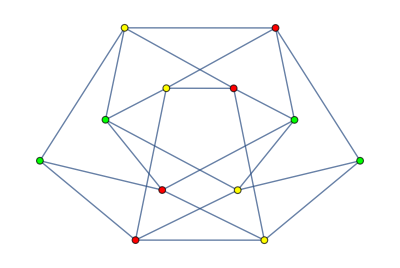
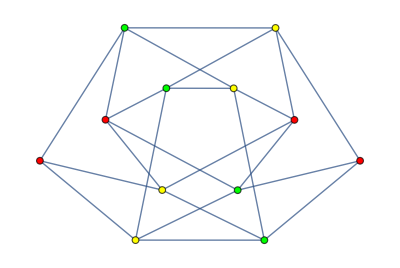
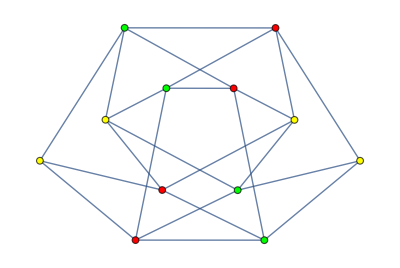
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allColorGraph[G,3]
```

```mathematica
countDCol[-Graphics-,4]
```

24

```mathematica
allColorGraph[-Graphics-,4];
```

```mathematica
graphGroebnerBase[-Graphics-,4]
```

{-1+x_4^4,x_3^3+x_3^2 x_4+x_3 x_4^2+x_4^3,x_2^2+x_2 x_3+x_3^2+x_2 x_4+x_3 x_4+x_4^2,x_1+x_2+x_3+x_4}

```mathematica
makeGraphPoly[-Graphics-,3]//TableForm
```

-1+x_1^3
-1+x_2^3
-1+x_3^3
-1+x_4^3
x_1^2+x_1 x_2+x_2^2
x_1^2+x_1 x_3+x_3^2
x_1^2+x_1 x_4+x_4^2
x_2^2+x_2 x_3+x_3^2
x_2^2+x_2 x_4+x_4^2
x_3^2+x_3 x_4+x_4^2

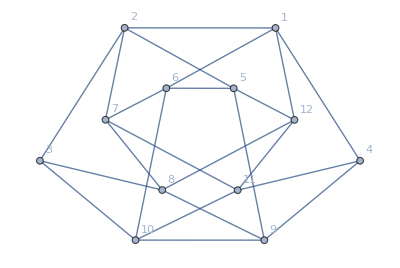

```mathematica
G =Graph[{1<->2,1<->4,1<->6,1<->12,2<->3,2<->5,2<->7,3<->8,3<->10,4<->9,4<->11,5<->6,5<->9,5<->12,6<->7,6<->10,7<->8,7<->11,8<->9,8<->12,9<->10,10<->11,11<->12},VertexLabels->All]
```

```mathematica
countDCol[G,1]
countDCol[G,2]
countDCol[G,3]
```

No es 1-coloreable

No es 2-coloreable

6

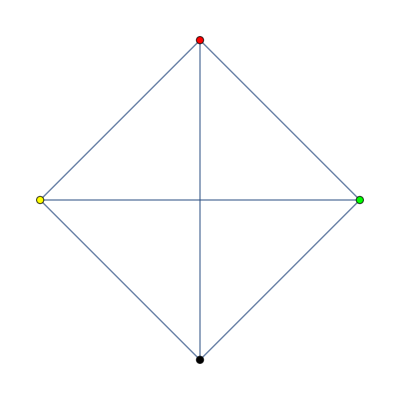

```mathematica
allColorGraph[-Graphics-,4][[1]]
```